## DIG-CSC 120: Programming in the Humanities

## Davidson College Dr. Jakub Kabala

## Coding Project 2

### Guidelines

Work in pairs on these problems, and only in your assigned pairs--you may not work alone, or with other pairs. If you come to office hours or to an appointment with me, you must come as a pair. Read “Pair Programming” document on Moodle/Course Documents.

Read instructions carefully. Formatting matters.

When writing a Module[...], do not repeat long chunks of code. Instead, make definitions along the way, and re-use the definitions. I will count off for repetitive code inside Modules[...].

No late penalties for Projects received by class on Thursday, Feb. 11

Hat Tip: This coding project was inspired by and based on Matthew Jockers, Text Analysis with R for Students of Literature (Springer, 2014)

### Problem 1: Gutenberg Prep

Choose some novel OTHER than Moby Dick that you find on the internet, and which interests you and your partner. You can browse here: http://www.gutenberg.org/ebooks/. NB:

Make sure the page you are importing is a Plain Text .TXT file. You do not want to import an .HTML file.

Make sure also that your novel has chapter headings.

#### Step 1

Using Import[] and your novel’s URL, save the text of a novel of your choosing to a symbol. This will be a string.

```mathematica
Alice=ToLowerCase[Import["http://www.gutenberg.org/files/11/11-0.txt"]];
```

#### Step 2

You now have a string which, unfortunately, contains lots of Gutenberg front matter and end matter. Using StringPosition[] and StringTake[], extract just the text of the novel. Save that extracted string to a new variable.

```mathematica
beginning=StringPosition[Alice,"chapter i.\n"][[1,1]]
```

1437

```mathematica
ending=StringPosition[Alice,"the end \n"][[1,2]]
```

145454

```mathematica
alicetext=StringTake[Alice,{beginning,ending}];
```

#### Step 3

Take a look at your novel and see how chapters begin and end. Using StringSplit[], split your novel string into strings representing chapters. You should now have a list of multiple strings (each one a chapter). Double check with the text of the novel to make sure your chapter strings actually correspond to the novel’s chapters. If they don’t, adjust your StringSplit[] code until they do. Save your list of chapters into a new symbol.

```mathematica
aliceChapters=StringSplit[alicetext,"\n\nchapter"];
```

### Problem 2: Word Frequency

Let’s define the frequency of a word in a text to be the measure of how many times per 100 that word appears in a text. For example, let’s imagine a boring text containing 15 words: 10 “the”s and 5 “and”s:
	
		“the the the the the the the the the the and and and and and”

The frequency of the word ‘and’ in this text would be (5/15) * 100 = 33.333

a) Write a Module[...] that will make at least two initial definitions:

a string representing a text

a string representing some word

and will calculate the frequency of that word in that text.

```mathematica
Module[{example,word,exampleWords},

example=aliceChapters[[1]];
word="alice";

exampleWords=TextWords[ToLowerCase[example]];
N[100*Count[exampleWords,word]/Length[exampleWords]]
]
```

1.25698

b) Using Table, ListLinePlot, and your Module[...] plot the frequency of two chosen words that interest you (and which you suspect might have some kind of relationship to each other) across all chapters of your chosen novel. Be sure to include plot and axes labels. Be sure your plot has an appropriate size.  

For example, here might be a plot of the frequencies of the words ‘whale’ and ‘ahab’ in Moby Dick:

-Graphics-

```mathematica
freqs=Table[Table[Module[{example,word,exampleWords},

example=text;
word=x;

exampleWords=TextWords[example];
N[100*Count[exampleWords,word]/Length[exampleWords]]
],{text,aliceChapters}],{x,{"alice","rabbit"}}]
```

{{1.25698,1.13422,1.34977,1.12952,1.60994,1.65512,2.17675,1.56501,2.05151,1.46128,0.849708,1.03676},{0.27933,0.141777,0.,0.414157,0.,0.,0.,0.24077,0.,0.0487092,0.424854,0.377003}}

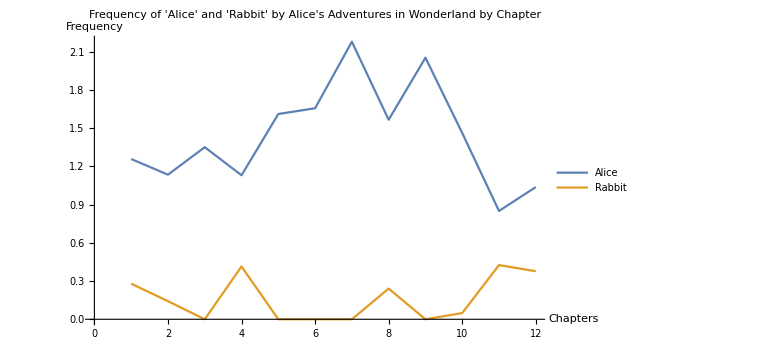

```mathematica
ListLinePlot[freqs,PlotLabel->"Frequency of 'Alice' and 'Rabbit' by Alice's Adventures in Wonderland by Chapter",PlotLegends-> {"Alice","Rabbit"},ImageSize->Large,AxesLabel->{"Chapters","Frequency"}]
```

c) Using Correlation[...], calculate the correlation between between the frequencies of your two words in the successive chapters of novel. Use the bootstrapping method to determine whether or not your correlation is significant. What does your result suggest about the structure of the novel?

```mathematica
Module[
{Alice2,alicetext2,aliceChapters2,word1,word2},
Alice2=ToLowerCase[Import["http://www.gutenberg.org/files/11/11-0.txt"]];
alicetext2=StringTake[Alice2,{beginning,ending}];
aliceChapters2=StringSplit[alicetext2,"\n\nchapter"];
word1="alice";
word2="rabbit";
N[Correlation[Table[Length[StringPosition[aliceChapters2[[x]],word2]],{x,Range[12]}],Table[Length[StringPosition[aliceChapters2[[x]],word1]],{x,Range[12]}]]]
]
```

-0.456547

```mathematica
Table[Table[Module[{example,word,exampleWords},

example=text;
word=x;

exampleWords=TextWords[example];
N[100*Count[exampleWords,word]/Length[exampleWords]]
],{text,aliceChapters}],{x,{"alice","rabbit"}}]
```

{{1.25698,1.13422,1.34977,1.12952,1.60994,1.65512,2.17675,1.56501,2.05151,1.46128,0.849708,1.03676},{0.27933,0.141777,0.,0.414157,0.,0.,0.,0.24077,0.,0.0487092,0.424854,0.377003}}

```mathematica
aliceList=Table[Module[{example,word,exampleWords},

example=text;
word="alice";

exampleWords=TextWords[example];
N[100*Count[exampleWords,word]/Length[exampleWords]]
],{text,aliceChapters}];
```

```mathematica
rabbitList=Table[Module[{example,word,exampleWords},

example=text;
word="rabbit";

exampleWords=TextWords[example];
N[100*Count[exampleWords,word]/Length[exampleWords]]
],{text,aliceChapters}];
```

```mathematica
correlation=Correlation[aliceList,rabbitList]
```

-0.766459

```mathematica
Correlation[RandomSample[aliceList],rabbitList]
```

0.153142

```mathematica
shuffle=Table[Correlation[RandomSample[aliceList],rabbitList],10000]
```

{-0.0570495,0.123728,9996,-0.0362311,0.00157145}
 |  |  |  |

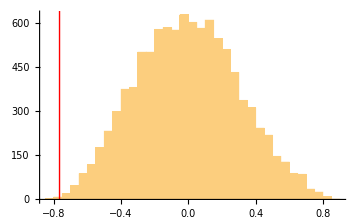

```mathematica
Histogram[shuffle,Epilog->{Red,Thick,Line[{{correlation,0},{correlation,800}}]},
ImageSize->Medium]
```

```mathematica
Mean[shuffle]
```

-0.00398396

```mathematica
correlation=Correlation[aliceList,rabbitList]
```

-0.766459

```mathematica
Mean[shuffle]-(StandardDeviation[shuffle]*2)
```

-0.605607

```mathematica
Mean[shuffle]-(StandardDeviation[shuffle]*3)
```

-0.906418

Our observed value of “correlation” is between 2 and 3 Standard Deviations away from the mean. This means that our value is not statistically significant since anything above 3 Standard Deviations is considered significant.

### Problem 3: Mean Word Usage

mean word usage is a measure of how many times, on average, a word gets used in a given text. For example, let’s imagine a boring text containing only 10 “the”s, 6 “and”s, and 5 “it”s:
	
		“the the the the the the the the the the and and and and and and it it it it it”
		
The mean word usage in this text would be (10 + 6 +5) / 3 =  7. This means that each word in the text gets used--on average--7 times.

a) Write a Module[...] that will make at least one local definition:

a string of text

and will then calculate the mean word usage within that text.

```mathematica
N[Length[StringSplit[aliceChapters[[1]]]]/Length[Union[StringSplit[aliceChapters[[1]]]]]]
```

2.7706

```mathematica
Module[{words},
words=StringSplit[aliceChapters[[1]]];
N[Length[words]/Length[Union[words]]]]
```

2.7706

b) Using Table[], ListLinePlot[], and your Module[...], plot the mean word usage in each chapter of your chosen novel. Be sure to include plot and axes labels. Be sure your plot has an appropriate size.

```mathematica
chapterNumber=Range[Length[aliceChapters]];
```

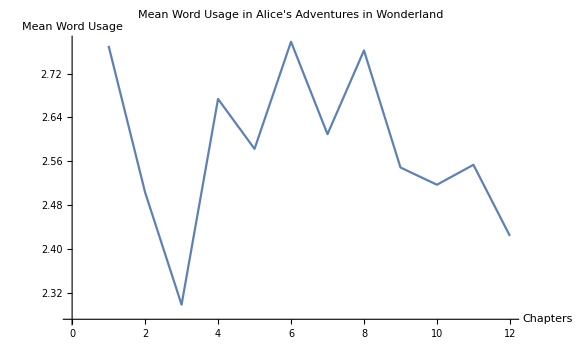

```mathematica
ListLinePlot[Table[Module[{words},
words=StringSplit[aliceChapters[[x]]];
N[Length[words]/Length[Union[words]]]
],{x,Range[Length[aliceChapters]]}],PlotLabel->"Mean Word Usage in Alice's Adventures in Wonderland",AxesLabel->{"Chapters","Mean Word Usage"},ImageSize->Large]
```

c) Calculate the correlation between the mean word usage and chapter length across all chapters in your chosen novel. Use bootstrapping to determine the significance of the correlation value. What does this result suggest about your author and the novel?

```mathematica
meanWord=Table[Module[{words},
words=StringSplit[aliceChapters[[x]]];
N[Length[words]/Length[Union[words]]]],{x,chapterNumber}];
```

```mathematica
chapterLength=Table[StringLength[aliceChapters[[x]]],{x,chapterNumber}];
```

```mathematica
cor2=Correlation[meanWord,chapterLength]
```

0.763212

```mathematica
shuffle2=Table[Correlation[RandomSample[meanWord],chapterLength],10000]
```

{-0.230512,0.182715,9996,0.325103,0.132556}
 |  |  |  |

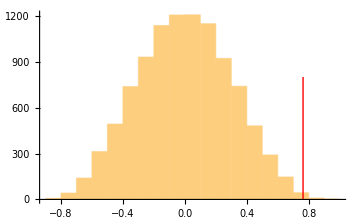

```mathematica
Histogram[shuffle2,Epilog->{Red,Thick,Line[{{cor2,0},{cor2,800}}]},
ImageSize->Medium]
```

```mathematica
Mean[shuffle2]+(StandardDeviation[shuffle2]*3)
```

0.904696

```mathematica
Mean[shuffle2]+(StandardDeviation[shuffle2]*2)
```

0.602933

Our observed value of “correlation” is between 2 and 3 Standard Deviations away from the mean. This means that our value is not statistically significant since anything above 3 Standard Deviations is considered significant.

### Problem 4: Type-Token Ratio

type-token ratio is the ratio of the number of unique words in a text (word types) to the total number of words in that text (word tokens). For example, the string: 

				“hi how are you hi how are you” 
				
contains 4 word types (‘hi’, ‘how’, ‘are’ and ‘you’) but 8 word tokens. Its type-token ratio 4/8 = 0.5.

a) Write a Module[...]  that will make at least one local definition:

a string of text

and will calculate the type-token ratio of that text.

```mathematica
Module[
{words},
words=StringSplit[aliceChapters[[1]]];
N[Length[Union[words]]/Length[words]]]
```

0.360933

b) Using Table[], ListLinePlot[], and your Module[...], plot the type-token ratio in each chapter of your chosen novel. Be sure to include plot and axes labels. Be sure your plot has an appropriate size.

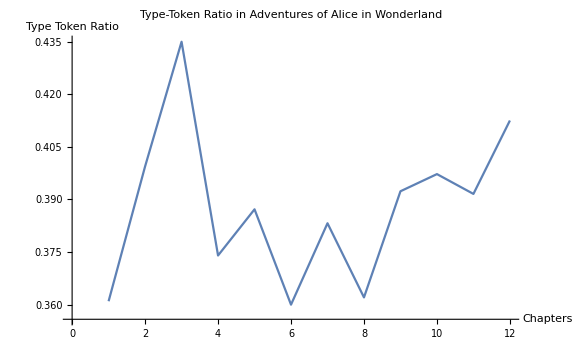

```mathematica
ratio=Table[Module[
{words},
words=StringSplit[aliceChapters[[x]]];
N[Length[Union[words]]/Length[words]]],{x,Range[Length[aliceChapters]]}];
ListLinePlot[ratio,PlotLabel->"Type-Token Ratio in Adventures of Alice in Wonderland",AxesLabel->{"Chapters","Type Token Ratio"},ImageSize->Large
]
```

c) Calculate the correlation between the type-token ratio and chapter length across your chosen novel. Use bootstrapping to determine the significance of the correlation value. What does this result suggest about your author and the novel?

```mathematica
typetoken= ratio=Table[Module[
{words},
words=StringSplit[aliceChapters[[x]]];
N[Length[Union[words]]/Length[words]]],{x,Range[Length[aliceChapters]]}];
chapterLength=Table[StringLength[aliceChapters[[x]]],{x,Range[Length[aliceChapters]]}];
Correlation[typetoken, chapterLength]
shuffled3=Table[Correlation[RandomSample[typetoken],chapterLength],10000];
```

-0.771263

```mathematica
Mean[shuffled3]-(StandardDeviation[shuffled3]*3)
```

-0.9051

```mathematica
Mean[shuffled3]-(StandardDeviation[shuffled3]*2)
```

-0.603432

Our observed value of correlation is between 2 and 3 Standard Deviations away from the mean. This means that our value is not statistically significant since anything above 3 Standard Deviations is considered significant.

### Problem 5: Hapax Legomena Count

A hapax legomenon is a word that occurs only ONCE in a given context. For example, the string: 

				“hi alice how are you hi how are you” 
				
contains ONE hapax legomenon: the word “alice.”

a) Write a Module[...] that will make at least one local definition:

a string of text

and will count the number of hapax legomena in that text.

```mathematica
Module[
{word},
word=StringSplit[aliceChapters[[1]]];
Length[Split[Sort[Table[Count[Sort[word],x],{x,Union[word]}]]][[1]]]]
```

537

b) Using Table[], ListLinePlot[], and your Module[...] plot the hapax legomena count for each chapter of your novel. Be sure to include plot and axes labels. Be sure your plot has an appropriate size.

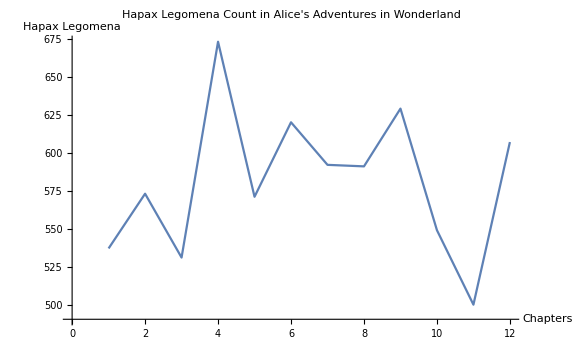

```mathematica
ListLinePlot[Table[Module[
{word},
word=StringSplit[aliceChapters[[y]]];
Length[Split[Sort[Table[Count[Sort[word],x],{x,Union[word]}]]][[1]]]],{y,Range[Length[aliceChapters]]}],PlotLabel->"Hapax Legomena Count in Alice's Adventures in Wonderland",AxesLabel->{"Chapters","Hapax Legomena"},ImageSize->Large
]
```

c) Calculate the correlation between the hapax legomena count and chapter length across your chosen novel. What does it suggest? Use bootstrapping to determine the significance of the correlation value. What does this result suggest about your author and the novel?

```mathematica
Hapax=Table[Module[
{word},
word=StringSplit[aliceChapters[[y]]];
Length[Split[Sort[Table[Count[Sort[word],x],{x,Union[word]}]]][[1]]]],{y,Range[Length[aliceChapters]]}];
N[Correlation[Hapax,chapterLength]]
shuffled4=Table[N[Correlation[RandomSample[Hapax],chapterLength]],10000];
```

0.800993

```mathematica
Mean[shuffled4]+(StandardDeviation[shuffled4]*3)
```

0.8902

```mathematica
Mean[shuffled4]+(StandardDeviation[shuffled4]*2)
```

0.592492

Our observed value of correlation is between 2 and 3 Standard Deviations away from the mean. This means that our value is not statistically significant since anything above 3 Standard Deviations is considered significant.